# Mini-Lecture: Mutual Information VS Correlation

For each x from 0 to 1 with a step of 0.01, we compute the corresponding y value based on the piecewise function and store the pair {x, y} in the data list.

```mathematica
data=Table[{x,Piecewise[{{x,0<x<=0.5},{0.5,x>0.5}}]},{x,0,1,0.01}];
```

Transposing swaps the rows and columns, so we end up with two lists: one for x values and one for y values.

```mathematica
transposedData=Transpose[data];
```

Calculate the correlation between the two lists (x and y values). The @@ operator is used to apply the Correlation function to the transposed data.

```mathematica
correlation=Correlation@@transposedData
```

0.894401

What if we find the correlation of the following piecewise instead?

y=|x|

```mathematica
correlation=Correlation@@Transpose@Table[{x,Piecewise[{{-x,x<0},{x,x>=0}}]},{x,-1,1,0.01}]
```

9.67943×10^-17

### Mutual Information

We find the mutual information for a deterministic function.

```mathematica
data=Table[{x,Piecewise[{{-x,x<0},{x,x>=0}}]},{x,-1,1,0.01}];
```

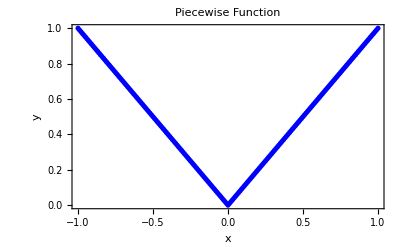

```mathematica
ListPlot[data,PlotStyle->Blue,Frame->True,Axes->True,FrameLabel->{"x","y"},PlotLabel->"Piecewise Function"]
```

```mathematica
transposedData=Transpose[data];
```

We can try and use a numerical method to check the mutual information of the table. Notice that if you make Nx larger, the mutual information increases. In fact it is infinite.

```mathematica
Nx=1000;

mutualInformation=N@Module[{data,hX,hY,hJoint},data=Table[{x,Piecewise[{{-x,x<0},{x,x>=0}}]},{x,-Nx,Nx,0.01}];{hX,hY,hJoint}=Entropy/@{data[[All,2]],data[[All,2]],data};hX+hY-hJoint]
```

11.1867

## Correlation Conversion to Mutual Information

We can use the following formula to convert it to something similar to mutual information in bits.

```mathematica
-Log[2,1-ρ^2]/2/.ρ->0.5
```

0.207519

If the correlation coefficient is 0.99 for example.

```mathematica
-Log[2,1-ρ^2]/2/.ρ->0.99
```

2.82554

```mathematica
-Log[2,1-ρ^2]/2/.ρ->0.999
```

4.48325

```mathematica
-Log[2,1-ρ^2]/2/.ρ->0.9
```

1.19796

When is this measure equal to 1.

```mathematica
-Log[2,1-ρ^2]/2/.ρ->0.8660260
```

1.